Hipóteses:
   * Gás dissolvido no óleo na sucção da bomba é 50% do Rs.
   * Pressão na sucção é aproximadamente igual a 70% da coluna de água.
   * Temperatura na sucção é igual à exterior.
   * Bo na sucção de 1,2.
   * Z é aproximadamente o mesmo nas condições de superfície e na sucção da bomba. O que leva a:

(P_suc V_suc)/T_suc=(P_std V_std)/T_std

```mathematica
Rsi=100.; (*m.b3/m.b3*)
RGO=200.; (*m.b3/m.b3*)
Pstd= 1.033; (* kgf/cm.b2*)
Tstd= 20.+273.15; (*K*)
Psuc= 2500. * 0.1 * 0.7; (* kgf/cm.b2*)
Tsuc= 5.+273.15; (*K*)
Vstd=(RGO-Rsi) + RGO*0.5; (*m.b3 de gás livre na sucção por m.b3 de óleo, em condição de superfície*)
```

```mathematica
Vsuc=Vstd Pstd/Psuc Tsuc/Tstd; (*m.b3*)
Print["Volume de gás livre na sucção: ",Vsuc," m.b3"]
```

Volume de gás livre na sucção: 0.840123 m.b3

```mathematica
Bo=1.2;
Gfr=Vsuc/(Vsuc+1*Bo);
Print["Fração de gás livre na sucção: ",Gfr*100," %"]
```

Fração de gás livre na sucção: 41.18 %

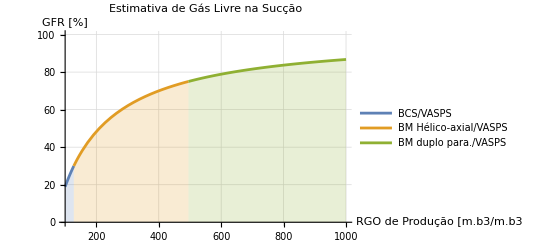

```mathematica
fGfr[RGO_]:=Block[{Vstd,Vsuc,Gfr},
Vstd=(RGO-Rsi) + RGO*0.5;
Vsuc=Vstd Pstd/Psuc Tsuc/Tstd;
Gfr=Vsuc/(Vsuc+1*Bo)*100.;
Gfr];
Plot[{ConditionalExpression[fGfr[RGO],fGfr[RGO]<=30],
ConditionalExpression[fGfr[RGO],fGfr[RGO]<=75 && fGfr[RGO]>30],
ConditionalExpression[fGfr[RGO],fGfr[RGO]>75]},
{RGO,100.,1000.},
Filling->{Axis},
PlotLegends->{"BCS/VASPS","BM Hélico-axial/VASPS","BM duplo para./VASPS"},
PlotRange->{{100,Automatic},{0,100}},
GridLines->Automatic,
PlotLabel->"Estimativa de Gás Livre na Sucção",
AxesLabel->{"RGO de Produção [m.b3/m.b3","GFR [%]"} ]
```